```mathematica
mybode=Function[{tf,f0,f1,db0,db1,ph0,ph1},
LogLinearPlot[{
20*Log10[Abs[tf[ⅈ 2π f]]],
(180/π*Arg[tf[ⅈ 2π f]]-ph0)/(ph1-ph0)*(db1-db0)+db0
},{f,f0,f1},PlotRange->{db0,db1},PlotTheme->"Monochrome",GridLines->Automatic,Frame->True
] //Print;
];
```

1/(1+C1 R0 s (1/(1+C1 R1 s)+(√10)/(10+C1 R1 s)+10/(100+C1 R1 s)))

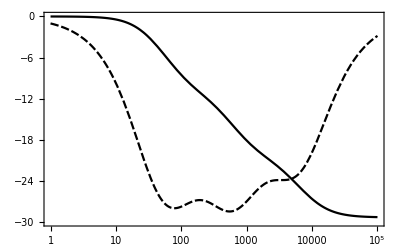

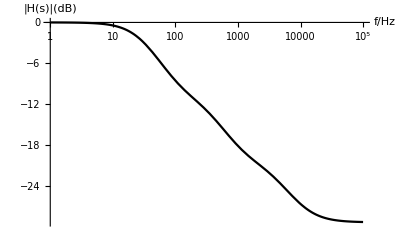

```mathematica
ClearAll[n,R1,R0,C1];
n=3;
hh1[s_,R1_,C1_]:=1/(∑_(i=0)^(n-1) 1/(R1/10^(i/2)+1/(s C1/10^(i/2))));
FullSimplify[1/(R0+hh1[s,R1,C1])*hh1[s,R1,C1]]
R1=1500;C1=0.000001;
h[s_]:=1/(2*R1+hh1[s,R1,C1])*hh1[s,R1,C1];
mybode[h,1,100000,-30,0,-45,0]
LogLinearPlot[20*Log10[Abs[h[ⅈ*2*π*f]]],{f,1,100000},PlotTheme->"Monochrome",AxesLabel->{"f/Hz","|H(s)|(dB)"},GridLines->Automatic]
```